```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI

```mathematica
DESY2s=Import["DESY2s.csv"];
```

```mathematica
DESY2sMean=Mean[DESY2s]
```

{-0.723974,-1.06981}

```mathematica
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
DESY2ssorted=Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}];
```

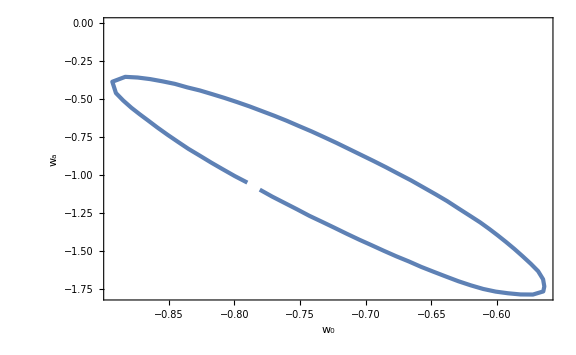

```mathematica
ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}]
```

```mathematica
e1[w0_]=3/2(1+w0);
e2[w0_,wa_]=-wa/(1+w0);
beta[w0_,wa_]=-e1[w0]+1/2 e2[w0,wa];
```

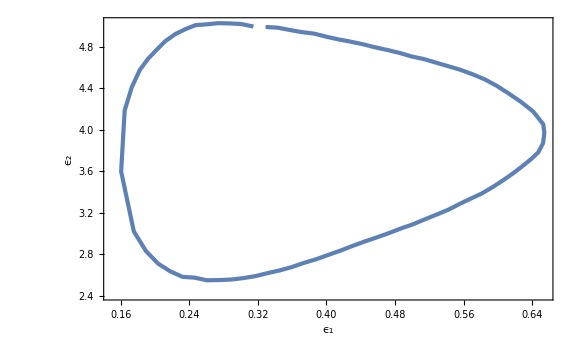

```mathematica
ListPlot[Map[{e1[#[[1]]],e2[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],Subscript[ϵ, 2]}]
```

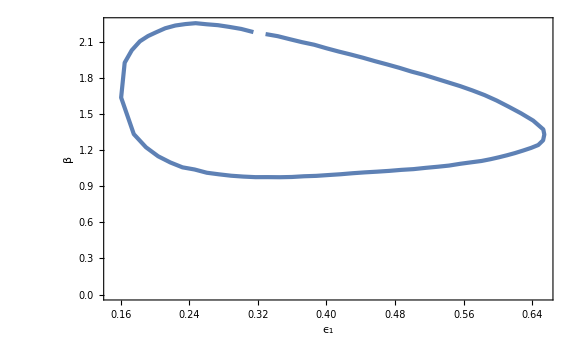

```mathematica
ListPlot[Map[{e1[#[[1]]],beta[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],β}]
```

```mathematica
H[x_]=A Cos[Sqrt[β/2]x];
```

```mathematica
V[x_]=3 H[x]^2-2 H'[x]^2//FullSimplify
```

1/2 A^2 (3-β+(3+β) Cos[√2 x √β])

```mathematica
eH[x_]=2(H'[x]/H[x])^2//FullSimplify
```

β Tan[(x √β)/(√2)]^2

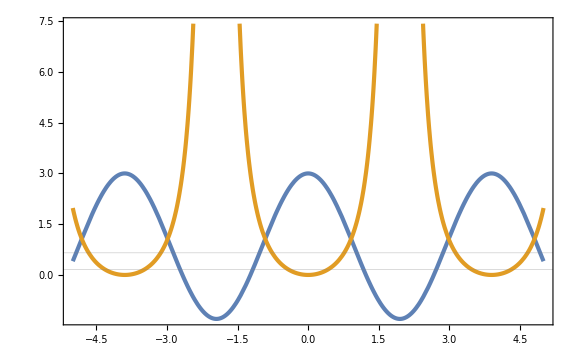

```mathematica
Plot[{V[x]/.{β->1.3,A->1},eH[x]/.{β->1.3}},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

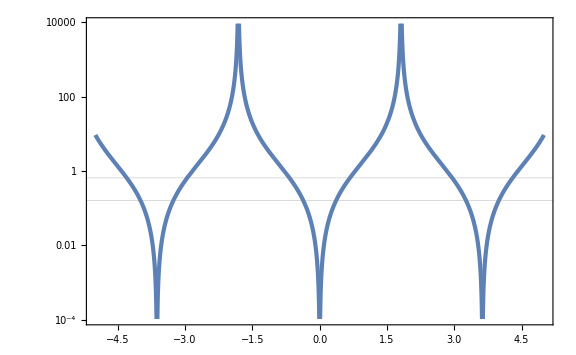

```mathematica
LogPlot[eH[x]/.{β->1.5,A->1},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

```mathematica
x0=x/.Solve[eH[x]==e10,x][[2]]/.{C[1]->0}
```

(√2 ArcTan[(√e10)/(√β)])/(√β)

```mathematica
As=A/.Solve[H[x0]==H0,A][[1]]
```

H0 √((e10+β)/β)

```mathematica
p0=Sqrt[2e10];
```

```mathematica
Ωs[x_,p_]=1/3(p^2/2+V[x]/H0^2)/.{A->As}
Htot[z_,x_,p_]=Sqrt[Ωm (1+z)^3(*+Ωr H0^2(1+z)^4*)+Ωs[x,p]]//Simplify
```

1/3 (p^2/2+((e10+β) (3-β+(3+β) Cos[√2 x √β]))/(2 β))

(√(p^2+6 (1+z)^3 Ωm+((e10+β) (3-β+(3+β) Cos[√2 x √β]))/β))/(√6)

```mathematica
pc=3086/1000 10^16(*m*);
H0s=(68 10^3)/(10^6 pc);
H0s//N
```

2.2035×10^-18

```mathematica
t0=H0s 138 10^8 60 60 24 36525/100;
t0//N
```

0.959613

```mathematica
EoM=Simplify[{x''[t]+3Htot[z[t],x[t],x'[t]]x'[t]+V'[x[t]]/H0^2==0/.{A->As},x[t0]==x0,x'[t0]==893/1000 p0,
z'[t]==-Htot[z[t],x[t],x'[t]](1+z[t]),z[t0]==0}/.{β->13/10,e10->4/10,Ωm->3/10}]
```

{√(3/2) x'[t] √(17/130 (17+43 Cos[√(13/5) x[t]])+9/5 (1+z[t])^3+x'[t]^2)+x''[t]==(731 Sin[√(13/5) x[t]])/(20 √65),x[46271331/48218750]==2 √(5/13) ArcTan[2/(√13)],2500 x'[46271331/48218750]==893 √5,z'[t]==-((1+z[t]) √(17/130 (17+43 Cos[√(13/5) x[t]])+9/5 (1+z[t])^3+x'[t]^2))/(√6),z[46271331/48218750]==0}

```mathematica
sol=NDSolve[EoM,{x[t],x'[t],z[t]},{t,0.09,t0},WorkingPrecision->30][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
zsol[t_]=z[t]/.sol;
Hsol[t_]:=Htot[zsol[t],xsol[t],psol[t]]/.{β->13/10,e10->4/10,Ωm->3/10};
esol[t_]:=psol[t]^2/(2 Hsol[t]^2);
```

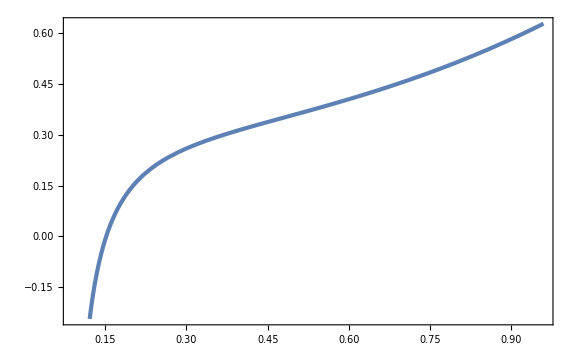

```mathematica
Plot[xsol[t],{t,0.09,t0}]
```

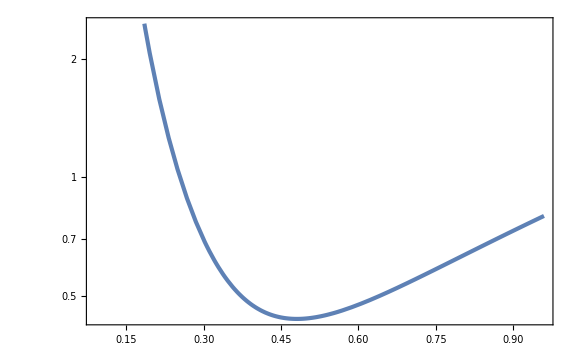

```mathematica
LogPlot[psol[t],{t,0.09,t0}]
```

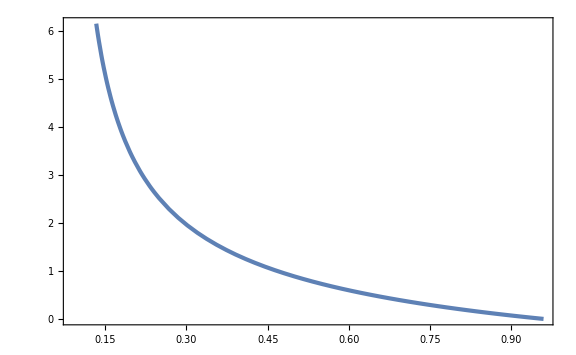

```mathematica
Plot[zsol[t],{t,0.09,t0}]
```

InterpolatingFunction::dmval: Input value {0.0900178} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

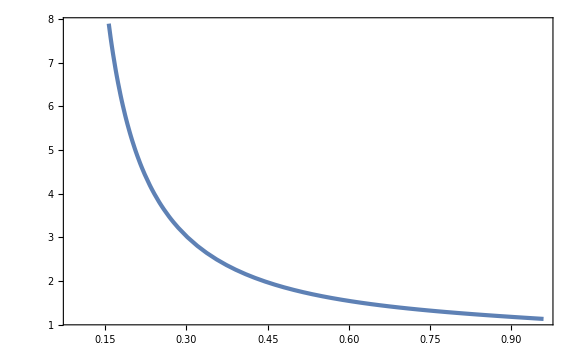

```mathematica
Plot[Hsol[t],{t,0.09,t0}]
```

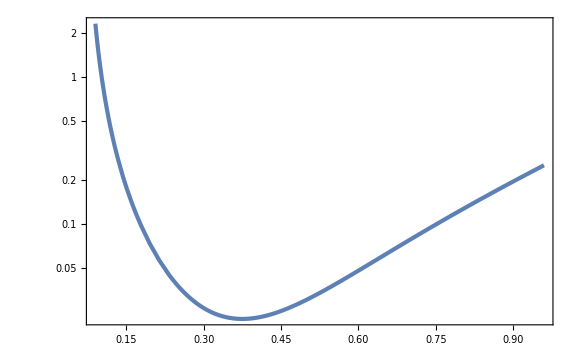

```mathematica
LogPlot[esol[t],{t,0.09,t0}]
```

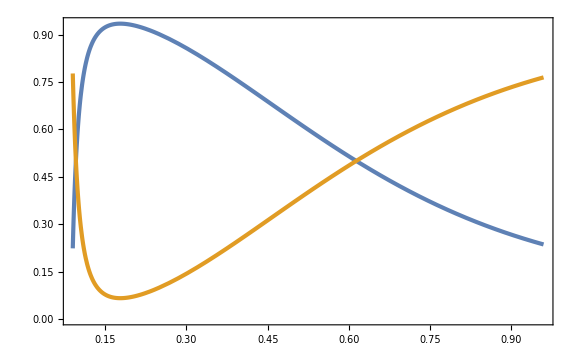

```mathematica
Plot[{(Ωm(1+zsol[t])^3)/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->13/10,e10->4/10,Ωm->3/10},Ωs[xsol[t],psol[t]]/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->13/10,e10->4/10,Ωm->3/10}},{t,0.09,t0}]
```